## Base code

```mathematica
e=1.6*10^-19; 
RibbonColors={Brown,Red,Orange,Yellow,Darker@Green,Blue,Purple,Gray,Black,White,LightGray};
```

### Create a SET network

```mathematica
(*Create NP internet with given physical parameters*)
CreateNPinternet[Np_,Nc_,Ni_,rP_,rT_,nT_,μBG_]:=Module[
	(*unit resistance, unit capacitance, and local variables*)
	{R0 = 25.*10^3, C0 = 1.6*10^-19,r,r′,dαβ},
	(*particle positions are randomly distributed in a circle*)
	posP=Catenate@(nT*rT+RandomPoint[Disk[{0, 0}, nT*rT], {Nc,Np}]);
	(*interconnect positions are spaced evenly along the circumference*)
	posI = Catenate@Table[nT*rT+nT*rT*{{Cos[th], Sin[th]},{Cos[th], -Sin[th]}}, {th, Pi/Ni, Pi, 2*Pi/Ni}]; 
	
	(*Calculate tunnel junction parameters: {location α,location β,mutual capacitance, tunnel conductance}*)	
	ppJs = DeleteMissing@Catenate@Catenate@Table[{r,r′}={x,y}+(c-1)*Np;
			dαβ=rP+Norm[posP_⟦r⟧-posP_⟦r′⟧];
			If[r>= r′,Missing[],{r,r′,rP^2/dαβ*C0,E^-(dαβ/rT)/R0}],(*particle-particle junction*)
		{x,Np},{y,Np},{c,Nc}];	
	ipJs = Table[
			dαβ=rP+Norm[posI_⟦i⟧-posP_⟦r⟧];
			{Np*Nc+i,r=Np(c-1)+x,rP^2/dαβ*C0,E^-(dαβ/rT)/R0},(*interconnect-particle junction*)
		{i,Ni},{c,Nc},{x,Np}];	
		
	gpJs = Table[{-2,r,rP*C0,0},{r,Np*Nc}];(*gate-particle junctions*)
	giJs = Table[{-2,Np*Nc+r,10.C0,0},{r,Ni}];(*gate-interconnect junctions*)
	
	biJs=Table[{-1,Np*Nc+r,0,100./R0},{r,Ni}];(*bias-interconnect junctions*)
	oiJs=Table[{0,Np*Nc+r,0,100./R0},{r,Ni}];(*output-interconnect junctions*)
	
	(*spatially varying background charge distribution*)
	m0=μBG*RandomReal[1,{Nc*Np+Ni}];
	]
(*Wire NP internet according to interconnectivity matrix, battery and sensory arrays*) 
WireNPinternet[W_,wB_,wO_]:=Module[{},
	nJs=Join[ppJs,Catenate@Catenate@Pick[ipJs,W,1]];(*neighbouring island-island junctions*)
	gJs=Join[gpJs,giJs];
	fJs=Catenate@Catenate@Pick[ipJs,W,0];(*floating junctions*)
	bJs=Pick[biJs,wB,1];(*bias junctions*)
	oJs=Pick[oiJs,wO,1];(*output junctions*)
	CreateSETnetwork[nJs,gJs,fJs,bJs,oJs];
	]
(*Create SET network from tunnel junction parameters*)
CreateSETnetwork[nJs_,gJs_,fJs_,bJs_,oJs_]:=Module[{s,r,r′,c,g,ℂ,G},
	(*Calculate charging potential matrix, conductivity matrix*)
	ℂ=ConstantArray[0,{Length@gJs,Length@gJs}];
	G=ConstantArray[0,{Length@gJs,Length@gJs}];
	Do[{r,r′,c,g}=j;
		ℂ_⟦r,r⟧+=c;ℂ_⟦r′,r′⟧+=c;ℂ_⟦r,r′⟧=ℂ_⟦r′,r⟧=-c;
		G_⟦r,r⟧+=g;G_⟦r′,r′⟧+=g;G_⟦r,r′⟧=G_⟦r′,r⟧=-g,
	{j,nJs}];
	Do[{s,r,c,g}=j;
		ℂ_⟦r,r⟧+=c;
		G_⟦r,r⟧+=g,
	{j,Join[gJs,bJs,oJs]}];
	Do[{r,r′,c,g}=j;
		ℂ_⟦r,r⟧+=c;ℂ_⟦r′,r′⟧+=c;ℂ_⟦r,r′⟧=ℂ_⟦r′,r⟧=-c,
	{j,fJs}];
	Φ=Inverse[ℂ/e];Φr=Diagonal[Φ];iG=PseudoInverse[G];
	
	φ=Max@Φ; (*critical potential*)
	
	(*Calculate coupling factors κ for determining stability regions*)
	κB=Sum[{s,r,c,g}=j;Φ_⟦r⟧c/e,{j,bJs}];
	κG=Sum[{s,r,c,g}=j;Φ_⟦r⟧c/e,{j,gJs}];
	ΔκG=Outer[Plus,κG,-κG];
	ΔκB=Outer[Plus,κB,-κB];
	
	(*Calculate barrier potential and locations of tunnel junctions*)
	If[Length@nJs==0, {αnJs,βnJs,ΦnJs,gnJs}={{},{},{},{}},
		{αnJs,βnJs,cs,gnJs}=nJsᵀ;
		ΦnJs=(Φr_⟦αnJs⟧+Φr_⟦βnJs⟧)/2-Extract[Φ,{βnJs,αnJs}ᵀ]];
	{αeJs,βeJs,cs,geJs}=Join[gJs,bJs,oJs]ᵀ;
	ΦeJs=Φr_⟦βeJs⟧/2;
	αβJs={Join[αnJs,αeJs],Join[βnJs,βeJs]}ᵀ;
	φ]
```

### Interesting wiring configurations in Ni=8 Nc=8 systems

#### Create colored graph

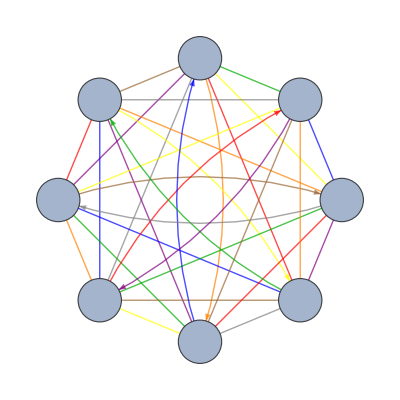

```mathematica
g0=Graph[{1,3,5,7,8,6,4,2},{1<->3,5->4,7<-> 6,8<->2,
1<->6,3<->5,7->2 ,8<->4,
1->8 ,3<->4,5<->7,6<->2,
1<->4,3-> 6,5<->2,7<->8,
1<->2,6->3,5<->8,7<->4,
8-> 1,3<->7,5<->6,4<->2,
1<->5,3<->8 ,2->7,6<->4,
1<->7,3<->2,4->5,8<->6}];
g1=Graph[{1,3,5,7,8,6,4,2},{1<->3,5->4,7<-> 6,8<->2,
1<->6,3<->5,7->2 ,8<->4,
1->8 ,3<->4,5<->7,6<->2,
1<->4,3-> 6,5<->2,7<->8,
1<->2,6->3,5<->8,7<->4,
8-> 1,3<->7,5<->6,4<->2,
1<->5,3<->8 ,2->7,6<->4,
1<->7,3<->2,4->5,8<->6},VertexSize->Large,VertexLabels->Placed["Name",Center],VertexCoordinates->Table[th=Pi/4+i*2*Pi/8;100*{Cos[th],Sin[th]},{i,8}],EdgeStyle->Gray,EdgeWeight->StringPartition["aaaabbbbccccddddeeeeffffgggghhhh",1]];

e1= EdgeList[g1];
(*Table[ColorData[38,x],{x,8}]*)
ec=Flatten@Table[e1⟦(x-1)*4+y⟧->RibbonColors⟦x⟧,{x,8},{y,4}];
g2=SetProperty[g1,EdgeStyle->ec];
g3=SetProperty[g2,EdgeStyle->Thick]
```

#### Obtain wiring address from path string

```mathematica
NPinternet[path_]:=
(
Vapp = {"bias"<->#}&/@Pick[signals,wB,_?Positive];
Imeas = {"ground"<->#}&/@Pick[signals,wO,_?Positive];
wC=ConstantArray[0,{Ni,Nc}]; (* [[s1,a]] *)
Table[ {a,b}=edge;ed=If[Abs[a+b]==9,a->b,a<->b];
cl=PropertyValue[{g1,ed},EdgeWeight];wC⟦{a,b},LetterNumber@cl⟧={1,1};
{signals⟦a⟧<->cl,signals⟦b⟧<->cl},{edge,Subsequences[path,{2}]}];
NPnet = Pick[ Table[Property[UndirectedEdge[signals⟦s⟧,clusters⟦c⟧],EdgeStyle->{Red,Green,Blue,Gray}⟦LEDconnectivity⟦s,c⟧⟧], {s,8},{c,8}] ,wC,_?Positive];

connections = Flatten[ { Vapp, Imeas, NPnet}];
nodes = Flatten[{Property["bias",VertexStyle-> White],Property["ground",VertexStyle->Black],signals,Table[Property[clusters⟦c⟧,VertexStyle->RibbonColors⟦c⟧],{c,8}]}];

internetG = Graph[nodes,connections,VertexSize->0.5,VertexCoordinates->Join[{{1,-2},{1,-7}},Table[{3,-i},{i,Ni}],Table[{7,-c},{c,Nc}]]];
Graph[internetG]
)
LEDconnectivity=({{1, 2, 4, 3, 1, 4, 3, 2}, {2, 4, 3, 2, 1, 1, 4, 3}, {1, 1, 2, 4, 4, 3, 2, 3}, {4, 3, 2, 3, 2, 1, 1, 4}, {4, 1, 1, 2, 3, 2, 3, 4}, {3, 2, 3, 4, 4, 2, 1, 1}, {3, 4, 1, 1, 2, 3, 4, 2}, {2, 3, 4, 1, 3, 4, 2, 1}});
```

```mathematica
NPinternet2[path_]:=
(
wC=ConstantArray[0,{Ni,Nc}]; (* [[s1,a]] *)
Table[ {a,b}=edge;ed=If[Abs[a+b]==9,a->b,a<->b];
cl=PropertyValue[{g1,ed},EdgeWeight];wC⟦{a,b},LetterNumber@cl⟧={1,1},{edge,Subsequences[path,{2}]}];
{ai}=FirstPosition[wC[[-1]],1];
{bi}=FirstPosition[wC[[1]],1];
)
```

```mathematica
NPinternet3[wC_]:=
(
Vapp = {"bias"<->#}&/@Pick[signals,wB,_?Positive];
Imeas = {"ground"<->#}&/@Pick[signals,wO,_?Positive];
NPnet = Pick[ Table[UndirectedEdge[signals⟦s⟧,clusters⟦c⟧], {s,8},{c,8}] ,wC,_?Positive];
connections = Flatten[ { Vapp, Imeas, NPnet}];
nodes = Flatten[{Property["bias",VertexStyle-> White],Property["ground",VertexStyle->Black],signals,Table[Property[clusters⟦c⟧,VertexStyle->RibbonColors⟦c⟧],{c,8}]}];

internetG = Graph[nodes,connections,VertexSize->0.5,VertexCoordinates->Join[{{1,-2},{1,-7}},Table[{3,-i},{i,Ni}],Table[{7,-c},{c,Nc}]]];
)
```

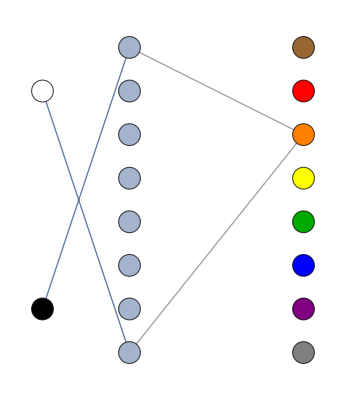

1566

```mathematica
Nc=8;
clusters = Alphabet[]⟦1;;Nc⟧;
signals= Table["s"<>ToString@i,{i,Ni=8}];
wO = IntegerDigits[128,2,Ni];
wB = IntegerDigits[1,2,Ni];
NPinternet/@FindPath[g0,1,8,1,All]
path8s=FindPath[g0,1,8,8,All];
abs=Table[NPinternet2[ path8s⟦i⟧];{ai,bi},{i,1957}];
wCs=Table[NPinternet2[ path8s⟦i⟧];wC,{i,1957}];
abPs=Flatten@Position[ Length/@(DeleteDuplicates/@abs),2];
Length@abPs
```

### Fitness of XOR functionality for an interesting wiring configuration

```mathematica
(*Evaluate 2-input logic in an interesting wiring configuration [Lawrence2018, pg. 60]*)
xorEvalpath[pathid_,Vb_,simulator_]:=
Block[{wC},
wC=wCs[[pathid]];
dat=
Table[
wC[[1,abs[[pathid]]]]=IntegerDigits[nwD,2,2];
WireNPinternet[wC,wB,wO];
Switch[simulator,
1,measureMC[Vb,0,10000,0*m0,0.001],
2,measureMF[Vb,0,1000,0*m0,0.001]
],{nwD,{1,2,3}}];
fits=Table[ If[ Max@dat[[;;,4]]<.01,FitnessQuality[dat[[;;,1]],Ideal],0] ,{Ideal,IdealOuts}]; 
Flatten@{fits,dat}
]
(*Fitness quality for logic functions similar to [Lawrence2018, pg. 80]*)
FitnessQuality[Measured_,Ideal_]:= Module[{max1,min1,max0,min0},
	{min1,max1}=MinMax@Pick[Measured,Ideal,1];
	{min0,max0}=MinMax@Pick[Measured,Ideal,0];
	(*add threshold and sanity check min0>-1*)
	If[min1>max0 && min0>-1,
		(min1-max0)/(max1-min0+Abs@min0+Ith),
		0.]
	]
```

### Orthodox theory at T=0 K

```mathematica
(* Tunnel activity at a microstate*)
tunnelIs[n_]:=(
Vr=Φ.(-m-n);
ΔFs=-Join[Abs[-Vr_⟦αnJs⟧+Vr_⟦βnJs⟧]-ΦnJs,Abs[-Vs_⟦1-αeJs⟧+Vr_⟦βeJs⟧]-ΦeJs];
Join[gnJs*Γ[-Vr_⟦αnJs⟧+Vr_⟦βnJs⟧,ΦnJs],geJs*Γ[-Vs_⟦1-αeJs⟧+Vr_⟦βeJs⟧,ΦeJs] ])
Γ[x_,y_]:=(Sign[x] Ramp[Abs[x]-y]); (*Rectifier*)
(*Monte-Carlo method*)
measureMC[Vb_,Vg_,steps_,n0_,precision_]:=Module[{IO=-1,IB=-1},
	err=1; nO=nB=t1=0;
	Vs=Flatten@{0.,Vb,Vg};
	n=n0;m=m0;
	Do[{s,r,Csr,g}=j;m_⟦r⟧+=-Csr*Vs_⟦1-s⟧/e,{j,Join[gJs,bJs,oJs]}];
	stepMC=0;
	Do[RandomJump[]; stepMC++;
		(* consider time after the first passing of electron from battery *)
		If[nB != 0, t1 += timeJ, nO = 0]; 
		If[timeJ==1,IB=IO=0;err=0,If[nO>10,err=relErr[IB=-e*nB/t1,IO=e*nO/t1] ] ];
		If[err<precision,Break[] ],
	steps];
	{IO,IB,Total@n,err,stepMC}]
RandomJump[]:= Module[{IabJs,Iab},
	(* calculate tunnel rates at every junction *)
	IabJs=tunnelIs[n];
	(* estimate tunneling time at every junction *)
	timeJs=Table[If[Iab==0,1,-e Log@RandomReal[]/Abs@Iab],{Iab,IabJs}];
	(* find junction that tunnels earliest *)
	{numJ}=Ordering[timeJs,1];
	Iab=IabJs_⟦numJ⟧;
	timeJ=timeJs_⟦numJ⟧;
	{a,b}=αβJs_⟦numJ⟧;
	Which[
		Iab>0,If[a>0,n_⟦a⟧-=1,nB-=1];If[b>0,n_⟦b⟧+=1],
		Iab<0,If[a>0,n_⟦a⟧+=1,nO+=1];If[b>0,n_⟦b⟧-=1]
		];
	]
(* relative error *)
Ith=10^-13; (*threshold current to set noise floor*)
relErr[I1_,I2_]:=Abs[I1-I2]/(Abs[I1]+Abs[I2]+Ith);
```

### Mean-Field simulation

```mathematica
(* confidence controlled multidimensional stepping method [Lawrence2018, pg. 76]*)
γ=1.2;λ=.5; (*gain and loss factors*)
measureMF[Vb_,Vg_,steps_,n0_,precision_]:=(
Vs=Flatten@{0.,Vb,Vg};
n=n0;m=m0;
Do[{s,r,Csr,g}=j;m_⟦r⟧+=-Csr*Vs_⟦1-s⟧/e,{j,Join[gJs,bJs,oJs]}];
δ=Normalize@ΔnΓ[n];
stepMF=0;
Do[takeStep[]; stepMF++;
If[Norm@tunnelIs[Round@n]==0,IO=IB=err=0;n=Round@n];
If[err<precision ,Break[] ],steps];
{IO,-IB,Total@n,err,stepMF})

(* take future step depending on alignment of the past step with the rate of change*)
takeStep[]:=(
Δn=Normalize@ΔnΓ[n];
δ=Table[
If[Δn_⟦r⟧ δ_⟦r⟧==0, Δn_⟦r⟧*φ/Φr_⟦r⟧,
If[Δn_⟦r⟧ δ_⟦r⟧> 0, Clip[γ*δ_⟦r⟧,Abs[Δn_⟦r⟧*φ/Φr_⟦r⟧]{-1,1}],-λ*δ_⟦r⟧] (*Allow larger steps for larger islands*) 
],{r,Length[n]}];(*Echo@{n,IO,IB,ΔnΓ[n,debug]};*)
n=n+δ)
(*calculate the rate of change at a macrostate [Lawrence2018, pg. 16]*)
ΔnΓ[n_?VectorQ]:= Module[{},p=n-Floor[n];
Vr=Φ.(-m-n)+p*Φr;ΔVsr=Outer[Plus,-Vs,Vr];(*ΔVrr=Outer[Plus,-Vr,Vr]+Outer[Plus,p,-p]*Φ*);
(*If[True, AppendTo[MFqs,n] ];*)
{IO0,IB0}={IO,IB};IO=0.;IB=0.;dI=0*n;
Do[{r,r′,c,g}=j;Iab=Ι[r,r′];dI_⟦r⟧-=Iab;dI_⟦r′⟧+=Iab,{j,nJs}];
Do[{s,r,c,g}=j;Iab=Ι[s,r];dI_⟦r⟧+=Iab;IB+=Iab,{j,Join[bJs,gJs]}];
Do[{s,r,c,g}=j;Iab=Ι[s,r];dI_⟦r⟧+=Iab;IO+=Iab,{j,oJs}];
(*If[True, AppendTo[IMFs,{IO,IB}] ];*)err=(*relErr[IB,IB0]+relErr[-IB,IO]+relErr[IO,IO0]+*)Norm[dI]/(Abs[IO]+Abs[IB]+Ith);
dI/e]
(*Mean current, [Lawrence2018, pg. 16]*)
P[α_,l_]:= If[l==0,1-p_⟦α⟧,p_⟦α⟧];
Ι[α_,β_]:=
g*If[α>0,
Block[{ΔV=Vr_⟦β⟧-p_⟦β⟧ Φ_⟦α,β⟧-Vr_⟦α⟧+p_⟦α⟧ Φ_⟦α,β⟧(*Subscript[ΔVrr, ⟦α,β⟧]*),ΔΦ′=Φr_⟦α⟧-Φ_⟦α,β⟧,ΔΦ=Φr_⟦β⟧-Φ_⟦α,β⟧},
∑_(l=0)^1 ∑_(l′=0)^1 P[α,l′]P[β,l]Γ[ΔV-l*ΔΦ+l′*ΔΦ′,(ΔΦ+ΔΦ′)/2] ],
Block[{P=p_⟦β⟧,ΔV=ΔVsr_⟦1-α,β⟧,ΔΦ=Φr_⟦β⟧},(1-P)*Γ[ΔV,ΔΦ/2]+P*Γ[ΔV-ΔΦ,ΔΦ/2] ]];
```

## Abundance of functionality

```mathematica
CreateNPinternet[Np=1,Nc=8,Ni=8,rP=1,rT=10,nT=10,μBG=0]
{wB,wO}=IdentityMatrix[Ni]⟦{1,-1}⟧;
```

```mathematica
IdealOuts={{0,0,1},{1,1,0},{1,0,1},{0,1,1},{0,1,0},{1,0,0}};
logics={"AND","XOR","A","B","!A.B","A.!B"}
```

```mathematica
abPs
```

{2,3,4,5,6,7,8,9,10,12,13,14,16,17,18,20,21,22,23,24,26,27,28,29,30,31,34,35,36,37,38,39,41,42,43,45,46,47,49,50,51,52,53,54,55,56,58,60,61,62,64,65,66,67,68,69,70,71,73,74,75,77,79,80,81,82,83,84,85,86,88,89,90,92,93,94,96,97,98,100,101,102,104,105,106,107,108,109,110,111,113,114,115,117,118,119,120,122,123,124,126,127,128,130,131,132,134,135,136,137,138,139,140,141,143,144,145,147,148,149,151,152,153,155,156,157,158,160,161,163,164,165,166,167,168,170,172,173,175,176,177,178,179,180,182,184,185,187,188,189,190,191,192,194,195,196,197,198,199,200,201,202,203,204,205,206,207,209,210,212,213,215,216,217,219,220,221,222,223,224,226,227,229,231,232,233,234,235,236,238,239,241,242,243,244,245,246,247,248,249,250,251,252,253,254,256,257,259,260,261,262,263,264,266,268,269,271,272,273,274,275,276,278,279,280,282,283,285,286,288,289,290,291,292,293,294,295,296,297,298,299,300,301,303,304,305,306,307,308,310,311,313,315,316,317,318,319,320,322,323,325,327,328,329,330,331,332,334,335,337,339,340,341,342,343,344,346,347,349,351,352,353,354,355,356,358,359,361,362,363,364,365,366,367,368,369,370,371,372,373,374,376,377,379,380,381,382,383,384,386,388,389,391,392,393,394,395,396,398,399,401,402,404,405,407,408,409,410,411,413,414,416,417,419,420,421,422,423,425,426,428,429,431,432,433,434,435,437,438,440,441,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,474,475,477,478,480,481,482,483,484,486,487,489,490,492,493,494,495,496,498,499,501,502,504,505,506,507,508,510,511,513,514,516,517,519,520,521,522,525,526,527,528,530,531,532,533,534,535,536,538,540,541,543,544,545,546,549,550,551,552,554,555,556,557,558,559,560,562,564,565,567,568,569,570,573,574,575,576,578,579,580,581,582,583,584,586,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,616,618,619,620,622,624,625,626,628,630,631,632,633,634,635,636,637,638,639,641,643,644,645,646,647,648,649,651,652,653,654,657,658,659,660,662,663,665,667,668,669,670,671,672,673,675,676,677,678,681,682,683,684,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,711,712,713,714,717,718,719,720,722,723,724,725,726,727,728,730,732,733,735,736,737,738,741,742,743,744,746,747,748,749,750,751,752,754,756,757,758,759,760,761,762,763,764,765,767,769,770,771,773,775,776,777,779,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,809,811,812,813,814,815,816,817,819,820,821,822,825,826,827,828,830,831,833,835,836,837,838,839,840,841,843,844,845,846,849,850,851,852,854,855,857,859,860,861,862,863,864,865,867,868,869,870,873,874,875,876,878,879,881,883,884,885,886,887,888,889,891,892,893,894,897,898,899,900,902,903,905,907,908,909,910,911,912,913,915,916,917,918,921,922,923,924,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,951,952,953,954,957,958,959,960,962,963,964,965,966,967,968,970,972,973,975,976,977,978,981,982,983,984,986,987,988,989,990,991,992,994,996,997,998,1000,1002,1003,1004,1006,1008,1009,1010,1012,1014,1015,1016,1017,1018,1019,1020,1021,1022,1024,1026,1027,1028,1030,1032,1033,1034,1036,1038,1039,1040,1041,1042,1043,1044,1045,1046,1048,1050,1051,1052,1054,1056,1057,1058,1060,1062,1063,1064,1065,1066,1067,1068,1069,1070,1072,1074,1075,1076,1078,1080,1081,1082,1084,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1151,1153,1154,1155,1157,1159,1160,1161,1163,1165,1166,1167,1168,1169,1170,1171,1172,1173,1175,1177,1178,1179,1181,1183,1184,1185,1187,1189,1190,1191,1192,1193,1194,1195,1196,1197,1199,1201,1202,1203,1205,1207,1208,1209,1211,1213,1214,1215,1216,1217,1218,1219,1220,1221,1223,1225,1226,1227,1229,1231,1232,1233,1235,1237,1238,1240,1241,1243,1244,1246,1247,1249,1250,1251,1252,1253,1254,1255,1257,1259,1260,1261,1262,1264,1265,1267,1268,1270,1271,1273,1274,1275,1276,1277,1278,1279,1281,1283,1284,1285,1286,1288,1289,1291,1292,1294,1295,1297,1298,1299,1300,1301,1302,1303,1305,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1335,1337,1338,1339,1341,1343,1344,1345,1347,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1362,1364,1365,1366,1367,1368,1369,1370,1372,1373,1375,1376,1378,1379,1381,1382,1383,1384,1386,1388,1389,1390,1391,1392,1393,1394,1396,1397,1399,1400,1402,1403,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1432,1433,1435,1436,1438,1439,1441,1442,1443,1444,1445,1446,1447,1449,1451,1452,1453,1454,1456,1457,1459,1460,1462,1463,1465,1466,1467,1468,1469,1470,1471,1473,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1488,1490,1491,1492,1494,1496,1497,1498,1500,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1530,1532,1533,1534,1535,1536,1537,1538,1540,1541,1543,1544,1546,1547,1549,1550,1551,1552,1554,1556,1557,1558,1559,1560,1561,1562,1564,1565,1567,1568,1570,1571,1573,1574,1575,1576,1578,1580,1581,1582,1583,1584,1585,1586,1588,1589,1591,1592,1594,1595,1597,1598,1599,1600,1602,1604,1605,1606,1607,1608,1609,1610,1612,1613,1615,1616,1618,1619,1621,1622,1623,1624,1626,1628,1629,1630,1631,1632,1633,1634,1636,1637,1639,1640,1642,1643,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1672,1673,1675,1676,1678,1679,1681,1682,1683,1684,1685,1686,1687,1689,1691,1692,1693,1694,1696,1697,1699,1700,1702,1703,1705,1706,1707,1708,1709,1710,1711,1713,1715,1716,1717,1719,1721,1722,1723,1725,1727,1728,1729,1731,1733,1734,1735,1736,1737,1738,1739,1740,1741,1743,1745,1746,1747,1749,1751,1752,1753,1755,1757,1758,1759,1760,1761,1762,1763,1764,1765,1767,1769,1770,1771,1773,1775,1776,1777,1779,1781,1782,1783,1784,1785,1786,1787,1788,1789,1791,1793,1794,1795,1797,1799,1800,1801,1803,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1872,1874,1875,1876,1878,1880,1881,1882,1884,1886,1887,1888,1889,1890,1891,1892,1893,1894,1896,1898,1899,1900,1902,1904,1905,1906,1908,1910,1911,1912,1913,1914,1915,1916,1917,1918,1920,1922,1923,1924,1926,1928,1929,1930,1932,1934,1935,1936,1937,1938,1939,1940,1941,1942,1944,1946,1947,1948,1950,1952,1953,1954,1956}

```mathematica
(*Monte-Carlo*)
```

```mathematica
xorEvalpath[abPs[[1]],4.,1]//AbsoluteTiming(*F1,F2...F6,IO_01,IB_01,Total@n_01,err_01,steps_01,IO_10,...,IO_11,...*)
```

{6.12726,{0.222386,0.,0.,0.396878,0.,0.,1.17753×10^-10,1.16547×10^-10,-75.,0.00514464,10000,2.40602×10^-10,2.40602×10^-10,-41.,0.,86,3.09439×10^-10,3.05885×10^-10,-76.,0.00577385,10000}}

```mathematica
(*Mean-field*)
```

```mathematica
xorEvalpath[abPs[[1]],4.,2]//AbsoluteTiming
```

{1.3232,{0.366892,0.,0.,0.260703,0.,0.,1.14699×10^-10,1.14688×10^-10,-76.5667,0.00062524,318,1.95065×10^-10,1.9541×10^-10,-40.0139,0.000701743,112,3.08164×10^-10,3.07792×10^-10,-76.5823,0.000768749,254}}